Exercise 1.3 a)

```mathematica
Remove["Global`*"]
n = {1,2,3,4};
k := (1-√(1-h))/(1-(1-h));
m = 1- k;
myTable = {};
y[x_] :=√x;
l[x_] := k*x+m;
delta[x_] := y[x] - l[x];

dx = Solve[D[delta[x],x] == 0,x]
AppendTo[myTable, {"h","x^*","ξ"}];
Do[
    h = 10^(-i);
    AppendTo[myTable, {h, N[x /. dx], N[delta[x]/.dx]}];
    
,{i,n}]
TableForm[myTable]
```

Exercise 1.3 b)

```mathematica
Clear[h]
derp[h_] := delta[x] /. dx
Series[derp[h], {h, 0, 2}]
Print["p: ", 2, ", c: ", 1/32]
```

Exercise 2.1

```mathematica
Remove["Global`*"]
data = {1,2,3,4,5}
(*data = {{1,1},{2,3},{3,2},,{4,4},{5,2}}*)
(*data[[1,1]] (*First pos in first point - PISEWISE*)*)


i = 2;
Do[
	Print[Plot[Piecewise[
	{{(x - data[[i-1]])/(data[[i]]-data[[i-1]]), data[[i-1]] < x < data[[i]]}, 
	{(data[[i+1]]-x)/(data[[i+1]]-data[[i]]), data[[i]] < x < data[[i+1]]}
	}], {x,1,5}]]	
,{i, 2, 4, 1}]
```

```mathematica
data[[i-1]]
```

Exercise 2.2
Estimate y at x = 4.2 using Linear interpolation

```mathematica
Remove["Global`*"]
xv = {1,2,3,4,5};
yv = {1,3,2,4,2};
data = Transpose[{xv,yv}];
f = Interpolation[yv, InterpolationOrder->1];
Plot[f[x],{x,1,5}]
f[4.2]
```

Exercise 2.3

```mathematica
Remove["Global`*"]
xv = {1,2,3,4,5};
yv = {1,3,2,4,2};
data = Transpose[{xv,yv}];

gd = ListPlot[data, PlotStyle->{Red, PointSize[Large]}, AxesLabel->{x, y}];


f = InterpolatingPolynomial[data, x]
Show[Plot[f,{x,1,5}, AxesLabel->{x, y}], gd]

Show[Plot[Interpolation[data, Method->"Hermite"][x],{x, 1, 5}, AxesLabel->{x, y}],gd]

p = Fit[data,{1, x, x^2,x^4,x^5},x];
Show[Plot[p,{x, 1, 5}, AxesLabel->{x, y}], gd]
```

Exercise 2.4

```mathematica
ArcLength[{Fit[data,{1, x, x^2,x^4,x^5},x]}, {x,0,5}]
```

Exercise 3.1

Solve,f(x,p) = -0.464835+1.46352 x-0.0735314 x^2

Fit, f(x,p) = -0.464835+1.46352 x-0.0735314 x^2

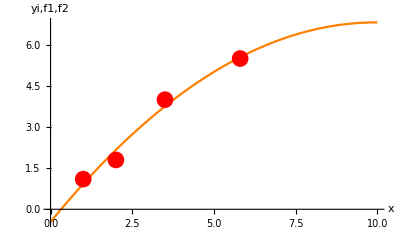

```mathematica
Remove["Global`*"]

xv = {1,2,3.5,5.8};
xy = {1.1,1.8,4,5.5};
data=Transpose[{xv,xy}];
n=Length[xv];
deg=2;

(* 3.1 A) *)
xv2=xv^2;
a=Transpose[{xv2,xv,Table[1,{i,1,n}]}];
Table[c[i],{i,0,deg}];
p=Reverse[Table[c[i],{i,0,deg}]];
f1=Reverse[Table[x^(i),{i,0,deg}]].p;

sol=Solve[Transpose[a].a.p==Transpose[a].xy,p];
Print["Solve,f(x,p) = ",N[f1/.sol[[1]]]]

(* 3.1 B) *)
f2 = Fit[data,{1,x,x^2},x];
Print["Fit, f(x,p) = ",f2]

(* 3.1 C) *)
Plot[Evaluate[{f1,f2}],{x, 0, 10}, PlotStyle->{Brown, Orange}, AxesLabel->{x, "yi,f1,f2"},Epilog->{Red, PointSize[0.03], Point[data]}]
```

Exercise 3.4

```mathematica
xv = {1,2,3.5,5.8};
y = {1.1,1.8,4,5.5};
```